```mathematica
(*ДЛЯ ЭЛЛИПСОИДА*)
Fun2[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=2*y[[4]];
y[[5]]=2*y[[5]];
y[[6]]=2*y[[6]];
Return[y];
];
Fun4[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=4*y[[4]];
y[[5]]=4*y[[5]];
y[[6]]=4*y[[6]];
Return[y];
];
Fun05[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,1,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=0.5*y[[4]];
y[[5]]=0.5*y[[5]];
y[[6]]=0.5*y[[6]];
Return[y];
];

vecE11=vecE22=vecv12=vecv23=vecG12={};
a1=3;
a2=1;
a3=1;
Δ=Sqrt[(a1^2+u)(a2^2+u)(a3^2+u)];
I2=N@2π*a1*a2*a3*Integrate[1/((a2^2+u)*Δ),{u,0,∞}];
I1=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)*Δ),{u,0,∞}];
I12=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)*(a2^2+u)*Δ),{u,0,∞}];
I11=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)^2*Δ),{u,0,∞}];
I22=N@2π*a1*a2*a3*Integrate[1/((a2^2+u)^2*Δ),{u,0,∞}];
s11=(3 a1^2)/(8π(1-v))*I11+(1-2v)/(8π(1-v))I1;
s22=s33=(3 a1^2)/(8π(1-v))*I22+(1-2v)/(8π(1-v))I2;
s55=s66=(3(a1^2+a2^2))/(16π(1-v))I12+(1-2v)/(16π(1-v))(I1+I2);
s44=a2^2/(8π(1-v))I22+(1-2v)/(8π(1-v))(I2);
s12=s13=(3*a2^2)/(8π(1-v))I12-(1-2v)/(8π(1-v))I1;
s21=s31=(5*v-1)/(15*(1-v));
s32=(5*v-1)/(15*(1-v));
s23=a2^2/(8π(1-v))I22-(1-2v)/(8π(1-v))(I2);

S={{s11,s12,s13,0,0,0},{s21,s22,s23,0,0,0},{s31,s32,s33,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s55,0},{0,0,0,0,0,s66}};
MatrixForm[S];
For[i=0,i≤100,i++,
Ee=3*10^9;
v=0.3;

a1=3;
a2=1;
a3=1;
c1=i/100;
c0=1-c1;
C11=(Ee(1-v))/((1+v)(1-2v));
C12=(Ee*v)/((1+v)(1-2v));
Cmatr={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K1=Ee/(3*(1-2*v));
mu1=Ee/(2*(1+v));
MatrixForm[Cmatr];

Ee1=55*10^9;
Ee2=45*10^9;
v12=0.2;
v23=0.25;
G12=20*10^9;
Ee3=Ee2;
G13=G12;
G23=Ee2/(2*(1+v23));
v13=v12;
v21=v12*Ee2/Ee1;
v31=v13*Ee3/Ee1;

B=(1-2v12*v21-v23^2-2*v12*v23*v21)/(Ee1*Ee2^2);
C11=(1-v23^2)/(Ee2^2*B); C22=(1-v12*v21)/(Ee1*Ee2*B);
C12=(v12*(1+v23))/(Ee1*Ee2*B);C23=(v23+v21*v12)/(Ee1*Ee2*B);
C22=(1-v12*v31)/(Ee1*Ee3*B); C23=(v23+v21*v13)/(Ee1*Ee2*B);
C66=G12;
Cmatr2={{C11,C12,C12,0,0,0},{C12,C22,C23,0,0,0},{C12,C23,C22,0,0,0},{0,0,0,(C22-C23)/2,0,0},{0,0,0,0,C66,0},{0,0,0,0,0,C66}};
MatrixForm[Cmatr2];

T1=Inverse[Fun4[(Fun05[IdentityMatrix[6]]+(S.(Fun2[Inverse[Fun4[Cmatr]]]).(Fun2[Cmatr2-Cmatr])))]];

MatrixForm[T1];
eps=Inverse[Fun4[(c0*Fun05[IdentityMatrix[6]]+c1*T1)]];
A1=T1.Fun2[eps];
MatrixForm[A1];
A0=Inverse[Fun4[c0*Fun05[IdentityMatrix[6]]-c1*T1]];
MatrixForm[A0];
Ccomp=Cmatr+(c1*(Cmatr2-Cmatr)).Fun2[A1];
MatrixForm[Ccomp];
Enew11=(Ccomp[[1]][[1]]*Ccomp[[2]][[2]]+Ccomp[[1]][[1]]Ccomp[[2]][[3]]-2*(Ccomp[[1]][[2]])^2)/(Ccomp[[2]][[2]]+Ccomp[[2]][[3]]);
Enew22 = (2*(Ccomp[[1]][[2]])^2*Ccomp[[2]][[2]]-2*(Ccomp[[1]][[2]])^2 Ccomp[[2]][[3]]+Ccomp[[1]][[1]]*(Ccomp[[2]][[3]])^2-Ccomp[[1]][[1]]*(Ccomp[[2]][[2]])^2)/((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[2]]);
vnew12=(Ccomp[[1]][[2]])/(Ccomp[[2]][[2]]+Ccomp[[2]][[3]]);
vnew23 =((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[3]])/((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[2]]);
Gnew12 =Ccomp[[6]][[6]];
AppendTo[vecE11,Enew11];
AppendTo[vecv12,vnew12];
AppendTo[vecE22,Enew22];
AppendTo[vecv23,vnew23];
AppendTo[vecG12,Gnew12];
];
```

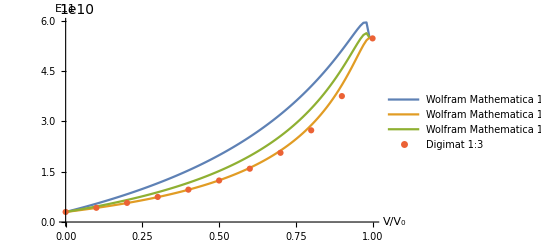

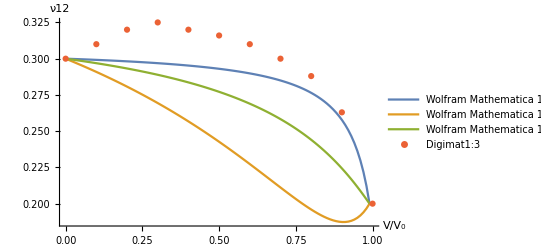

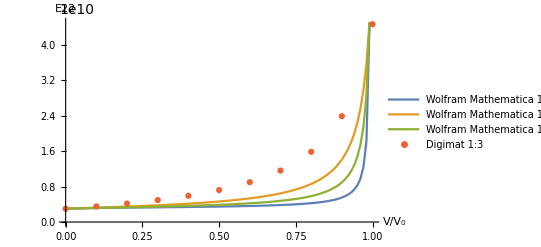

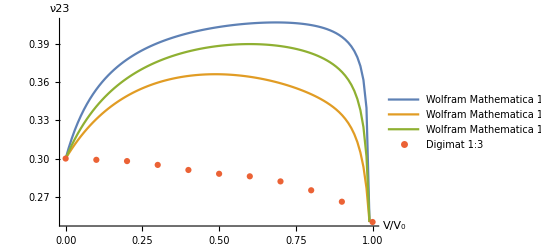

```mathematica
DigimatDataE11={{0,3*10^9},{0.1,4.24*10^9},{0.2,5.71*10^9},{0.3,7.48*10^9},{0.4,9.65*10^9},{0.5,12.38*10^9},{0.6,15.9*10^9},{0.7,20.64*10^9},{0.8,27.35*10^9},{0.9,37.55*10^9},{1,5.476*10^10}};
DigimatDataE22={{0,3*10^9},{0.1,3.53*10^9},{0.2,4.17*10^9},{0.3,4.94*10^9},{0.4,5.92*10^9},{0.5,7.21*10^9},{0.6,8.99*10^9},{0.7,11.6*10^9},{0.8,15.83*10^9},{0.9,23.86*10^9},{1,4.46*10^10}};
DigimatDatav12={{0,0.3},{0.1,0.31},{0.2,0.32},{0.3,0.325},{0.4,0.32},{0.5,0.316},{0.6,0.31},{0.7,0.3},{0.8,0.288},{0.9,0.263},{1,0.2}};
DigimatDatav23={{0,0.3},{0.1,0.299},{0.2,0.298},{0.3,0.295},{0.4,0.291},{0.5,0.288},{0.6,0.286},{0.7,0.282},{0.8,0.275},{0.9,0.266},{1,0.25}};
x={};
dataE={};
datav={};
For[i=0,i<Length[vecE11],i++,
AppendTo[x,i/Length[vecE11]];
];
For[i=1,i<Length[vecE11],i++,
(*AppendTo[dataE,{x[[i]],vecE[[i]]}];
AppendTo[datav,{x[[i]],vecv[[i]]}];*)
];










vecE112=vecE222=vecv122=vecv232=vecG122={};
a1=2;
a2=1;
a3=1;
Δ=Sqrt[(a1^2+u)(a2^2+u)(a3^2+u)];
I2=N@2π*a1*a2*a3*Integrate[1/((a2^2+u)*Δ),{u,0,∞}];
I1=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)*Δ),{u,0,∞}];
I12=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)*(a2^2+u)*Δ),{u,0,∞}];
I11=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)^2*Δ),{u,0,∞}];
I22=N@2π*a1*a2*a3*Integrate[1/((a2^2+u)^2*Δ),{u,0,∞}];
s11=(3 a1^2)/(8π(1-v))*I11+(1-2v)/(8π(1-v))I1;
s22=s33=(3 a1^2)/(8π(1-v))*I22+(1-2v)/(8π(1-v))I2;
s55=s66=(3(a1^2+a2^2))/(16π(1-v))I12+(1-2v)/(16π(1-v))(I1+I2);
s44=a2^2/(8π(1-v))I22+(1-2v)/(8π(1-v))(I2);
s12=s13=(3*a2^2)/(8π(1-v))I12-(1-2v)/(8π(1-v))I1;
s21=s31=(5*v-1)/(15*(1-v));
s32=(5*v-1)/(15*(1-v));
s23=a2^2/(8π(1-v))I22-(1-2v)/(8π(1-v))(I2);

S={{s11,s12,s13,0,0,0},{s21,s22,s23,0,0,0},{s31,s32,s33,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s55,0},{0,0,0,0,0,s66}};
MatrixForm[S];
For[i=0,i≤100,i++,
Ee=3*10^9;
v=0.3;

a1=2;
a2=1;
a3=1;
c1=i/100;
c0=1-c1;
C11=(Ee(1-v))/((1+v)(1-2v));
C12=(Ee*v)/((1+v)(1-2v));
Cmatr={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K1=Ee/(3*(1-2*v));
mu1=Ee/(2*(1+v));
MatrixForm[Cmatr];

Ee1=55*10^9;
Ee2=45*10^9;
v12=0.2;
v23=0.25;
G12=20*10^9;
Ee3=Ee2;
G13=G12;
G23=Ee2/(2*(1+v23));
v13=v12;
v21=v12*Ee2/Ee1;
v31=v13*Ee3/Ee1;

B=(1-2v12*v21-v23^2-2*v12*v23*v21)/(Ee1*Ee2^2);
C11=(1-v23^2)/(Ee2^2*B); C22=(1-v12*v21)/(Ee1*Ee2*B);
C12=(v12*(1+v23))/(Ee1*Ee2*B);C23=(v23+v21*v12)/(Ee1*Ee2*B);
C22=(1-v12*v31)/(Ee1*Ee3*B); C23=(v23+v21*v13)/(Ee1*Ee2*B);
C66=G12;
Cmatr2={{C11,C12,C12,0,0,0},{C12,C22,C23,0,0,0},{C12,C23,C22,0,0,0},{0,0,0,(C22-C23)/2,0,0},{0,0,0,0,C66,0},{0,0,0,0,0,C66}};
MatrixForm[Cmatr2];

T1=Inverse[Fun4[(Fun05[IdentityMatrix[6]]+(S.(Fun2[Inverse[Fun4[Cmatr]]]).(Fun2[Cmatr2-Cmatr])))]];

MatrixForm[T1];
eps=Inverse[Fun4[(c0*Fun05[IdentityMatrix[6]]+c1*T1)]];
A1=T1.Fun2[eps];
MatrixForm[A1];
A0=Inverse[Fun4[c0*Fun05[IdentityMatrix[6]]-c1*T1]];
MatrixForm[A0];
Ccomp=Cmatr+(c1*(Cmatr2-Cmatr)).Fun2[A1];
MatrixForm[Ccomp];
Enew11=(Ccomp[[1]][[1]]*Ccomp[[2]][[2]]+Ccomp[[1]][[1]]Ccomp[[2]][[3]]-2*(Ccomp[[1]][[2]])^2)/(Ccomp[[2]][[2]]+Ccomp[[2]][[3]]);
Enew22 = (2*(Ccomp[[1]][[2]])^2*Ccomp[[2]][[2]]-2*(Ccomp[[1]][[2]])^2 Ccomp[[2]][[3]]+Ccomp[[1]][[1]]*(Ccomp[[2]][[3]])^2-Ccomp[[1]][[1]]*(Ccomp[[2]][[2]])^2)/((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[2]]);
vnew12=(Ccomp[[1]][[2]])/(Ccomp[[2]][[2]]+Ccomp[[2]][[3]]);
vnew23 =((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[3]])/((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[2]]);
Gnew12 =Ccomp[[6]][[6]];
AppendTo[vecE112,Enew11];
AppendTo[vecv122,vnew12];
AppendTo[vecE222,Enew22];
AppendTo[vecv232,vnew23];
AppendTo[vecG122,Gnew12];
];












vecE115=vecE225=vecv125=vecv235=vecG125={};
a1=5;
a2=1;
a3=1;
Δ=Sqrt[(a1^2+u)(a2^2+u)(a3^2+u)];
I2=N@2π*a1*a2*a3*Integrate[1/((a2^2+u)*Δ),{u,0,∞}];
I1=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)*Δ),{u,0,∞}];
I12=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)*(a2^2+u)*Δ),{u,0,∞}];
I11=N@2π*a1*a2*a3*Integrate[1/((a1^2+u)^2*Δ),{u,0,∞}];
I22=N@2π*a1*a2*a3*Integrate[1/((a2^2+u)^2*Δ),{u,0,∞}];
s11=(3 a1^2)/(8π(1-v))*I11+(1-2v)/(8π(1-v))I1;
s22=s33=(3 a1^2)/(8π(1-v))*I22+(1-2v)/(8π(1-v))I2;
s55=s66=(3(a1^2+a2^2))/(16π(1-v))I12+(1-2v)/(16π(1-v))(I1+I2);
s44=a2^2/(8π(1-v))I22+(1-2v)/(8π(1-v))(I2);
s12=s13=(3*a2^2)/(8π(1-v))I12-(1-2v)/(8π(1-v))I1;
s21=s31=(5*v-1)/(15*(1-v));
s32=(5*v-1)/(15*(1-v));
s23=a2^2/(8π(1-v))I22-(1-2v)/(8π(1-v))(I2);

S={{s11,s12,s13,0,0,0},{s21,s22,s23,0,0,0},{s31,s32,s33,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s55,0},{0,0,0,0,0,s66}};
MatrixForm[S];
For[i=0,i≤100,i++,
Ee=3*10^9;
v=0.3;

a1=5;
a2=1;
a3=1;
c1=i/100;
c0=1-c1;
C11=(Ee(1-v))/((1+v)(1-2v));
C12=(Ee*v)/((1+v)(1-2v));
Cmatr={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K1=Ee/(3*(1-2*v));
mu1=Ee/(2*(1+v));
MatrixForm[Cmatr];

Ee1=55*10^9;
Ee2=45*10^9;
v12=0.2;
v23=0.25;
G12=20*10^9;
Ee3=Ee2;
G13=G12;
G23=Ee2/(2*(1+v23));
v13=v12;
v21=v12*Ee2/Ee1;
v31=v13*Ee3/Ee1;

B=(1-2v12*v21-v23^2-2*v12*v23*v21)/(Ee1*Ee2^2);
C11=(1-v23^2)/(Ee2^2*B); C22=(1-v12*v21)/(Ee1*Ee2*B);
C12=(v12*(1+v23))/(Ee1*Ee2*B);C23=(v23+v21*v12)/(Ee1*Ee2*B);
C22=(1-v12*v31)/(Ee1*Ee3*B); C23=(v23+v21*v13)/(Ee1*Ee2*B);
C66=G12;
Cmatr2={{C11,C12,C12,0,0,0},{C12,C22,C23,0,0,0},{C12,C23,C22,0,0,0},{0,0,0,(C22-C23)/2,0,0},{0,0,0,0,C66,0},{0,0,0,0,0,C66}};
MatrixForm[Cmatr2];

T1=Inverse[Fun4[(Fun05[IdentityMatrix[6]]+(S.(Fun2[Inverse[Fun4[Cmatr]]]).(Fun2[Cmatr2-Cmatr])))]];

MatrixForm[T1];
eps=Inverse[Fun4[(c0*Fun05[IdentityMatrix[6]]+c1*T1)]];
A1=T1.Fun2[eps];
MatrixForm[A1];
A0=Inverse[Fun4[c0*Fun05[IdentityMatrix[6]]-c1*T1]];
MatrixForm[A0];
Ccomp=Cmatr+(c1*(Cmatr2-Cmatr)).Fun2[A1];
MatrixForm[Ccomp];
Enew11=(Ccomp[[1]][[1]]*Ccomp[[2]][[2]]+Ccomp[[1]][[1]]Ccomp[[2]][[3]]-2*(Ccomp[[1]][[2]])^2)/(Ccomp[[2]][[2]]+Ccomp[[2]][[3]]);
Enew22 = (2*(Ccomp[[1]][[2]])^2*Ccomp[[2]][[2]]-2*(Ccomp[[1]][[2]])^2 Ccomp[[2]][[3]]+Ccomp[[1]][[1]]*(Ccomp[[2]][[3]])^2-Ccomp[[1]][[1]]*(Ccomp[[2]][[2]])^2)/((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[2]]);
vnew12=(Ccomp[[1]][[2]])/(Ccomp[[2]][[2]]+Ccomp[[2]][[3]]);
vnew23 =((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[3]])/((Ccomp[[1]][[2]])^2-Ccomp[[1]][[1]]*Ccomp[[2]][[2]]);
Gnew12 =Ccomp[[6]][[6]];
AppendTo[vecE115,Enew11];
AppendTo[vecv125,vnew12];
AppendTo[vecE225,Enew22];
AppendTo[vecv235,vnew23];
AppendTo[vecG125,Gnew12];
];










ListPlot[{Table[{x[[i]],vecE115[[i]]},{i,Length[x]}],Table[{x[[i]],vecE112[[i]]},{i,Length[x]}],Table[{x[[i]],vecE11[[i]]},{i,Length[x]}],Table[{DigimatDataE11[[i]][[1]],DigimatDataE11[[i]][[2]]},{i,Length[DigimatDataE11]}]},Joined->{True,True,True,False},AxesLabel->{V/Subscript[V, 0],E11},PlotLegends->{"Wolfram Mathematica 1:5","Wolfram Mathematica 1:2","Wolfram Mathematica 1:3","Digimat 1:3"}]
ListPlot[{Table[{x[[i]],vecv125[[i]]},{i,Length[x]}],Table[{x[[i]],vecv122[[i]]},{i,Length[x]}],Table[{x[[i]],vecv12[[i]]},{i,Length[x]}],Table[{DigimatDatav12[[i]][[1]],DigimatDatav12[[i]][[2]]},{i,Length[DigimatDatav12]}]},Joined->{True,True,True,False},AxesLabel->{V/Subscript[V, 0],ν12},PlotLegends->{"Wolfram Mathematica 1:5","Wolfram Mathematica 1:2","Wolfram Mathematica 1:3","Digimat1:3"}]
ListPlot[{Table[{x[[i]],vecE225[[i]]},{i,Length[x]}],Table[{x[[i]],vecE222[[i]]},{i,Length[x]}],Table[{x[[i]],vecE22[[i]]},{i,Length[x]}],Table[{DigimatDataE22[[i]][[1]],DigimatDataE22[[i]][[2]]},{i,Length[DigimatDataE22]}]},Joined->{True,True,True,False},AxesLabel->{V/Subscript[V, 0],E22},PlotLegends->{"Wolfram Mathematica 1:5","Wolfram Mathematica 1:2","Wolfram Mathematica 1:3","Digimat 1:3"},PlotRange->All]
ListPlot[{Table[{x[[i]],vecv235[[i]]},{i,Length[x]}],Table[{x[[i]],vecv232[[i]]},{i,Length[x]}],Table[{x[[i]],vecv23[[i]]},{i,Length[x]}],Table[{DigimatDatav23[[i]][[1]],DigimatDatav23[[i]][[2]]},{i,Length[DigimatDatav23]}]},Joined->{True,True,True,False},AxesLabel->{V/Subscript[V, 0],ν23},PlotLegends->{"Wolfram Mathematica 1:5","Wolfram Mathematica 1:2","Wolfram Mathematica 1:3","Digimat 1:3"}]
```

```mathematica
MatrixForm[Ccomp]
```

(6.0259×10^10 | 1.31474×10^10 | 1.31474×10^10 | 0. | 0. | 0.
1.31474×10^10 | 5.08685×10^10 | 1.48685×10^10 | 0. | 0. | 0.
1.31474×10^10 | 1.48685×10^10 | 5.08685×10^10 | 0. | 0. | 0.
0. | 0. | 0. | 1.8×10^10 | 0. | 0.
0. | 0. | 0. | 0. | 2.×10^10 | 0.
0. | 0. | 0. | 0. | 0. | 2.×10^10)